## Associated Code

```mathematica
bresenhamLine[p0_,p1_]:=Module[{dx,dy,sx,sy,err,newp},{dx,dy}=Abs[p1-p0];
{sx,sy}=Sign[p1-p0];
err=dx-dy;
newp[{x_,y_}]:=With[{e2=2 err},{If[e2>-dy,err-=dy;x+sx,x],If[e2<dx,err+=dx;y+sy,y]}];
NestWhileList[newp,p0,#=!=p1&,1]];
```

```mathematica
findSym[mask_,option_:False]:=Block[{imd,nx,ny,points,weights,mass,centerOfMass,pointsCom,diag,inertia,v1,v2},
imd=Transpose@ImageData[mask];(*here we transpose the image data*)
{nx,ny}=Dimensions[imd];(*dimensions of the image*)
points=Tuples[{Range[nx],Reverse@Range[ny]}];(*x-y coordinates on the image*)
weights=Flatten[imd];(*vector of imagedata*)
centerOfMass=ImageMeasurements[mask,"IntensityCentroid"];(*here we calculate the x-y coordinate of the center of mass*)
pointsCom=(Subtract[#,centerOfMass]&/@points) weights;(*we subtract from each point the center of mass.This gives us a vector of n number of points the {x,y} coordinates of which are displacements from the centroids.We multiply this resulting matrix with the intensity vector.This gives us a vector consisting of two coordinates which are x,y displacments from centroid for each point in the grid*)diag=Total[(#.#)&/@pointsCom];(*sum of the {x,y}.{x,y} from above. gives a single value*)
inertia=Table[KroneckerDelta[i,j] diag-Total[(#[[i]] #[[j]])&/@pointsCom],{i,2},{j,2}];(*inertia*)
{v1,v2}=Eigenvectors[inertia];(*extracting eigenvectors from inertia*)
(*Print["center of Mass: ",centerOfMass,"\n","pt1 : ",v1+centerOfMass,"\n","pt2 : ",v2+centerOfMass];*)If[option,Print@Show[mask,Graphics[{{Thick,Dashed,XYZColor[0,0,1,0.6],InfiniteLine[{v2+centerOfMass,centerOfMass}]},{Thick,Dashed,XYZColor[1,0,0,0.6],InfiniteLine[{v1+centerOfMass,centerOfMass}]},
{Darker@XYZColor[0,1,0,0.5],PointSize[Large],Point[centerOfMass]},
Red,Point[v1+centerOfMass],Blue,Point[v2+centerOfMass]}]]
];
{centerOfMass,v1,v2}];

maskToRegion[mask_]:=Block[{pixelvaluepos,tour,pixelposordered},
pixelvaluepos=PixelValuePositions[MorphologicalPerimeter@mask,1];
tour=Last@FindShortestTour[pixelvaluepos];
pixelposordered=Part[pixelvaluepos,tour];
{pixelposordered,BoundaryMeshRegion[N@pixelvaluepos,Line@tour]}
];

bisectMask[mask_,option_:False]:=Block[{centerofMass,v1,v2,pixelordered,ℛ1,ℛ2,temp,pt1,pt2,list,trimList,npixelordered,nf,ptslocation,firstPreMask,secondPreMask,dim,pt3,pt4},
dim=First@ImageDimensions[mask];
{centerofMass,v1,v2}=findSym[mask];
{pixelordered,ℛ1}=maskToRegion[mask];

ℛ2=InfiniteLine[{centerofMass,centerofMass+v2}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:>arg]&);

trimList[ls_]:=Module[{p=ls,pairs,firstelem=First@ls,dist,maxdist},
pairs={firstelem,#}&/@p;
dist=EuclideanDistance[##]&@@@pairs;
maxdist=Max@dist;
pairs[[First@@Position[dist,maxdist]]]
]/;Length@ls>2;

{pt3,pt4}=trimList[list]/.trimList[arg__]:>arg;

ℛ2=InfiniteLine[{centerofMass,centerofMass+v1}];
list=(RegionIntersection[ℛ2,#]&/@MeshPrimitives[ℛ1,1]//Cases[#,Point[arg_]:>arg]&);
{pt1,pt2}=trimList[list]/.trimList[arg__]:>arg;

If[option,
temp=Show[HighlightMesh[ℛ1,{Style[1,Directive[XYZColor[0,0,1,0.9]]],Style[2,Directive[XYZColor[0,0,1,0.18]]]}],Graphics[{Red,PointSize[Large],Point@pt1,PointSize[Large],Darker@Green,Point@pt2,Thick,Dashed,XYZColor[1,0,0,0.5],ℛ2,Blue,Point@centerofMass}]]
];
npixelordered=N@pixelordered;
nf=Nearest[npixelordered];
ptslocation=Flatten@Position[npixelordered,Flatten@nf[pt1]|Flatten@nf[pt2]];
firstPreMask=PadRight[#,Length@#+1,#]&@Part[pixelordered,First@ptslocation;;Last@ptslocation]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;
secondPreMask=Join[pixelordered[[;;First@ptslocation+1]],pixelordered[[Last@ptslocation+1;;]]]//Graphics[{White,Line@#},PlotRange->{{0,dim},{0,dim}}]&//Rasterize[#,"Image",Background->Black,ImageSize->{{dim},{dim}}]&//FillingTransform@*Binarize;
Switch[option,True,Join[{temp},{centerofMass},pt1,pt2,pt3,pt4],_,Join[{centerofMass},pt1,pt2,pt3,pt4]]
];
```

## Maps

```mathematica
(* imports *)
images=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - cropped.tif"][[1;;160]];
masks1=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\C10 - masks.tif"][[1;;160]];
mask1=masks1[[125]];
```

```mathematica
masks2=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\D11 - masks.tiff"][[;;160]];
mask2=masks2[[-1]];
Clear[masks2];
```

```mathematica
masks3=Import["C:\\Users\\aliha\\Desktop\\brachyury - optic flow\\F10 - masks.tiff"];
mask3=masks3[[-1]];
Clear[masks3];
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx";
res1=sim;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim3-filter20.mx";
res2=sim;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim2.mx";
res3=sim;
```

```mathematica
meanFlowField[flowfield_]:=Normal@GroupBy[Flatten[Thread/@flowfield,1],First->Last,Mean]/.Rule-> List;
```

```mathematica
ptsRotateToMask[pts_,mask_]:=With[{dim=Last[ImageDimensions[mask]]},
Abs[{0,dim}-#]&/@Reverse[pts,2]
];
```

```mathematica
{meanflow1,meanflow2,meanflow3}=meanFlowField/@{res1,res2,res3};
```

```mathematica
(* we have mean flow fields for all the three aggregates *)
```

```mathematica
{pts1,vec1}=Transpose@meanflow1;
{pts2,vec2}=Transpose@meanflow2;
{pts3,vec3}=Transpose@meanflow3;
```

```mathematica
pts1rot=ptsRotateToMask[pts1,mask1];
{cim1,dxyim1}=N@*Mean/@{pts1rot,RotationTransform[Pi/2]@vec1};
HighlightImage[mask1,{Red,pts1rot,Blue,Thick,InfiniteLine[{cim1+dxyim1,cim1}]},ImageSize->Small]
```

-Graphics-

```mathematica
pts2rot=ptsRotateToMask[pts2,mask2];
{cim2,dxyim2}=N@*Mean/@{pts2rot,RotationTransform[Pi/2]@vec2};
HighlightImage[mask2,{Red,pts2rot,Blue,Thick,InfiniteLine[{cim2+dxyim2,cim2}]},ImageSize->Small]
```

-Graphics-

```mathematica
pts3rot=ptsRotateToMask[pts3,mask3];
{cim3,dxyim3}=N@*Mean/@{pts3rot,RotationTransform[Pi/2]@vec3};
HighlightImage[mask3,{Red,pts3rot,Blue,Thick,InfiniteLine[{cim3+dxyim3,cim3}]},ImageSize->Small]
```

-Graphics-

```mathematica
(*lets rotate mask2 onto mask1 *)
```

```mathematica
(m1=ImagePad[mask1,{{59,60},{65,64}}])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(m2=ImagePad[ImageRotate[mask2,-VectorAngle[dxyim1,dxyim2]],{{55,54},{38,37}}])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(m3=ImageRotate[mask3,-VectorAngle[dxyim1,dxyim3]])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
SameQ@@ImageDimensions/@{m1,m2,m3}
```

True

```mathematica
HighlightImage[m1,{Red,m2,Blue,m3},ImageSize->Small]
```

-Graphics-

```mathematica
(*m1 is reference to which other images need to be aligned to*)
```

```mathematica
{HighlightImage[m1,m2,ImageSize->Small],HighlightImage[m1,m3,ImageSize->Small]}
```

{-Graphics-,-Graphics-}

```mathematica
(align1=ImageAlign[m1,m2,Method->"MeanSquareGradientDescent",
TransformationClass->"Affine",Background->0])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
(align2=ImageAlign[m1,m3,Method->"MeanSquareGradientDescent",
TransformationClass->"Affine",Background->0])//Image[#,ImageSize->Tiny]&
```

-Graphics-

```mathematica
HighlightImage[m1,{Red,align1,Blue,align2},ImageSize->200]
```

-Graphics-

```mathematica
interpBoundary[img_,div_]:=Module[{ℛ,polygon,t,interp,sub},
ℛ=ImageMesh[img,Method->"Exact"];
polygon=Append[#,First@#]&@MeshCoordinates[ℛ][[ MeshCells[ℛ,2][[1,1]] ]];t=Prepend[Accumulate[Norm/@Differences[polygon]],0.];interp=Interpolation[Transpose[{t,polygon}],InterpolationOrder->1,PeriodicInterpolation->True];sub=Subdivide[interp[[1,1,1]],interp[[1,1,2]],div];interp[sub]
];
```

```mathematica
interpPeri1=interpBoundary[m1,400];
interpPeri2=interpBoundary[m2,400];
interpPeri3=interpBoundary[m3,400];
```

```mathematica
{err1,transF1}=FindGeometricTransform[interpPeri1,interpPeri2,Method->"FindFit",TransformationClass->"Affine"]
```

{4.7663,TransformationFunction[(1.16057 | 0.17751 | -62.6178
-0.0956376 | 1.00478 | 17.356
0. | 0. | 1.)]}

```mathematica
{err2,transF2}=FindGeometricTransform[interpPeri1,interpPeri3,Method->"FindFit",TransformationClass->"Affine"]
```

{4.98608,TransformationFunction[(1.07426 | 0.103792 | -37.4726
-0.0253317 | 0.999644 | 6.73643
0. | 0. | 1.)]}

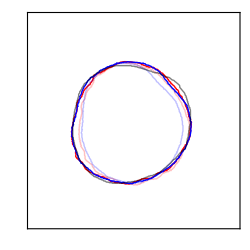

```mathematica
Graphics[
{{Thick,Red,Opacity[0.25],Line@interpPeri3},{Red,Thick,Line[transF2@interpPeri3]},
(*{GrayLevel[0.4],Arrowheads[Small],Arrow[{#,transF2@#}&/@interpPeri2]},*)
{Thick,Blue,Opacity[0.25],Line@interpPeri2},{Thick,Blue,Line[transF1@interpPeri2]},
{Thick,Opacity[0.5],Black,Line@interpPeri1}},PlotRange->{{0,382},{0,382}},ImageSize->250,
Frame->True,FrameTicks->False
]
```

```mathematica
(* till above we have a transformation matrix (affine transformation class) obtained from image masks that we can use to transform the points from one image to another *)
```

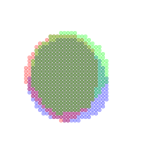

```mathematica
Graphics[{Opacity[0.3],Blue,Point@pts1,Red,Point@pts2,Green,Point@pts3},PlotRange->{{0,280},{0,280}},ImageSize->150]
```

```mathematica
{rotatedm1,rotatedm2,rotatedm3}=ImageRotate[#,Pi/2]&/@{m1,m2,m3};
```

```mathematica
Show[ImageRotate[mask1,Pi/2],Graphics[{XYZColor[0,1,1,0.5],PointSize[0.025],Point@pts1}],ImageSize-> Tiny]
```

-Graphics-

```mathematica
Show[ImageRotate[mask2,Pi/2],Graphics[{Green,Point@pts2}],ImageSize->Tiny]
```

-Graphics-

```mathematica
Show[ImageRotate[mask3,Pi/2],Graphics[{Red,Point@pts3}],ImageSize->Tiny]
```

-Graphics-

```mathematica
(*translate and rotate pts -> this is because of how we created m3 and m2 *)
```

```mathematica
transformPts[image_,pts_,θ_]:=Block[{centim,dxy,ptsR,ptsTR},
centim=ImageMeasurements[image,"IntensityCentroid"];
ptsR= RotationTransform[θ][pts];
dxy=centim-Mean[ptsR];
ptsTR=#+dxy&/@ptsR
];

transformVec[vec_,θ_]:=Block[{ptsR,ptsTR},
ptsR= RotationTransform[θ,Mean@vec][vec]
];
```

```mathematica
(*translate points from reference image for translation (image padding) *)
```

```mathematica
centrotatedRef=ImageMeasurements[rotatedm1,"IntensityCentroid"];
meanRefPts=N[Mean@pts1];
dxy=centrotatedRef-meanRefPts;
pts1F=transformPts[rotatedm1,pts1,0.];
```

```mathematica
Show[rotatedm1,Graphics[{XYZColor[1,0,0,0.80],Point@pts1F}],ImageSize->Small]
```

-Graphics-

```mathematica
(*rotate and translate points to align with reference *)
```

```mathematica
pts3TR=transformPts[rotatedm3,pts3,-VectorAngle[dxyim1,dxyim3]];
Show[rotatedm3,Graphics[{Blue,Point@pts3TR}],ImageSize->Small]
```

-Graphics-

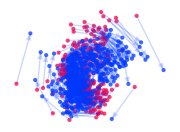

```mathematica
vec3R=transformVec[vec3,-π/4.0];
Graphics[{XYZColor[1,0,0,0.75],Point@vec3,Green,Point@(Mean[vec3]),XYZColor[0,0,1,0.75],Point@vec3R,
Opacity[0.2],Arrow/@Thread[{vec3,vec3R}]},ImageSize->Small]
```

```mathematica
(*now apply the geometric transform to diffuse flowfield within the reference bounds *)
```

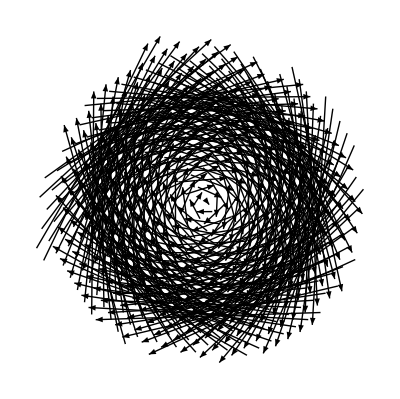

```mathematica
Graphics[{Arrowheads[Tiny],Arrow/@Thread[{pts3TR,RotationTransform[-π/2.0,Mean@pts3TR]@pts3TR}]}]
```

```mathematica
vec3RF=With[{mean=Mean[transF2[vec3R]]},
#-mean&/@transF2[vec3R]
];
```

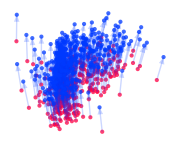

```mathematica
Graphics[{XYZColor[1,0,0,0.75],Point@vec3R,XYZColor[0,0,1,0.75],Point@vec3RF,
Opacity[0.2],Arrow/@Thread[{vec3R,vec3RF}]},ImageSize->Small]
```

```mathematica
pts3F=(RotationTransform[π/2,Mean@#][#])&@transF2[RotationTransform[-π/2,Mean@pts3TR]@pts3TR];
Show[rotatedm3,Graphics[{Blue,Point@pts3TR,XYZColor[0,1,0,0.75],Point@pts3F}],
ImageSize-> 200]
```

-Graphics-

```mathematica
(*the pts from the image transform well onto the reference *)
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[0,1,0,0.70],Point@pts3F,Red,Point@pts1F}],ImageSize->Small]
```

-Graphics-

```mathematica
(*rotate and translate points to align with reference *)
```

```mathematica
pts2TR=transformPts[rotatedm2,pts2,-VectorAngle[dxyim1,dxyim2]];
Show[rotatedm2,Graphics[{Blue,Point@pts2TR}],ImageSize->Small]
```

-Graphics-

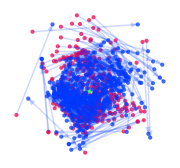

```mathematica
vec2R=transformVec[vec2,-2.2Pi/5];
Graphics[{XYZColor[1,0,0,0.75],Point@vec2,Black,Green,Point@(Mean[vec2]),XYZColor[0,0,1,0.75],Point@vec2R,
Opacity[0.2],Arrow/@Thread[{vec2,vec2R}]},ImageSize->Small]
```

```mathematica
(*now apply the geometric transform *)
```

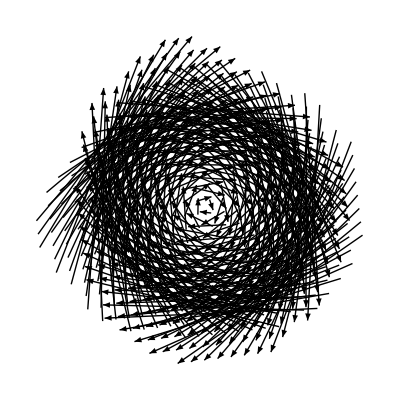

```mathematica
Graphics[{Arrowheads[Tiny],Arrow/@Thread[{pts2TR,RotationTransform[-π/2.0,Mean@pts2TR]@pts2TR}]}]
```

```mathematica
vec2RF=With[{mean=Mean[transF1[vec2R]]},
#-mean&/@transF1[vec2R]
];
```

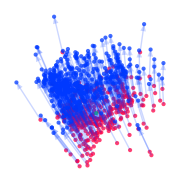

```mathematica
Graphics[{XYZColor[1,0,0,0.75],Point@vec2R,Black,Green,Point@(Mean[vec2R]),XYZColor[0,0,1,0.75],Point@vec2RF,
Opacity[0.2],Arrow/@Thread[{vec2R,vec2RF}]},ImageSize->Small]
```

```mathematica
pts2F=(RotationTransform[π/2,Mean@#][#])&@transF1[RotationTransform[-π/2,Mean@pts2TR]@pts2TR];
```

```mathematica
Show[rotatedm2,Graphics[{Blue,Point@pts2TR,XYZColor[1,0,0,0.75],Point@pts2F}],ImageSize-> 200]
```

-Graphics-

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[1,0,0,0.75],Point@pts2F,Cyan,Point@pts1F}],ImageSize->250]
```

-Graphics-

```mathematica
(*the pts from the image transforms  well onto the reference *)
```

```mathematica
Show[rotatedm1,Graphics[{PointSize[0.015],XYZColor[1,0,0,0.75],Point@pts2F,Cyan,Point@pts1F,,XYZColor[0,1,0,0.5],Point@pts3F}],ImageSize->250]
```

-Graphics-

### Velocity Profile

```mathematica
{flowfieldref,flowfield2,flowfield3}=MapThread[Thread[{Round@#1,#2}]&,{{pts1F,pts2F,pts3F},{vec1,vec2RF,vec3RF}}];
totalflow=(flowfieldref~Join~flowfield3~Join~flowfield2);
meanflow=Normal@GroupBy[totalflow,First-> Last,Mean]/. Rule -> List;
meanflowF=Thread[{(x↦x-dxy)/@#[[1]],#[[2]] }]&@Transpose[meanflow];
```

```mathematica
midimage=Ceiling[1/2Length[images]];
With[{reg=ConvexHullMesh@pts1},
Image[ImageRotate[
Rasterize[Show[
ImageRotate[SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[masks1[[5]],10],"Real"],.5]],Pi/2],
ListStreamPlot[meanflowF,
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],StreamPoints->Fine,
StreamColorFunction->"Rainbow",StreamStyle->Thickness[0.006]],
ImageSize->Large],"Image",ImageResolution->500],
-Pi/2],ImageSize->Medium]
]
```

-Graphics-

```mathematica
(*DumpSave["C:\\Users\\aliha\\Desktop\\optic flow\\meanflow.mx",meanflowF]*)
```

### Strain-Rate Map

```mathematica
Clear[g,gfilter,g1,g2,g3];
```

```mathematica
(* we can average the strain map for the aggregates *)
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim1-strain.mx";
resstrain1=strain;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim2-strain.mx";
resstrain3=strain;
<<"C:\\Users\\aliha\\Desktop\\optic flow\\sim3-strain.mx";
resstrain2=strain;
```

```mathematica
{g1,g2,g3}=Map[p↦{#[[2,1]],GeometricTransformation[Circle[#[[1]],#[[2,2]]+{1.0,1.0}],#[[2,3]]]}&/@Flatten[p,1]/.XYZColor[x__,0.33]:> XYZColor[x,0.66],
{resstrain1,resstrain2,resstrain3}];
```

```mathematica
p2=Flatten[resstrain2[[All,All,1]],1];
p3=Flatten[resstrain3[[All,All,1]],1];
```

```mathematica
g2f=(GeometricTransformation[#,RotationTransform[-2.2π/5,Mean@p2]]&/@g2)/.XYZColor[x__,0.33]:> XYZColor[x,0.66];
g3f=(GeometricTransformation[#,RotationTransform[-π/4.0,Mean@p3]]&/@g3)/.XYZColor[x__,0.33]:> XYZColor[x,0.66];
```

```mathematica
g=(g1~Join~g2f~Join~g3f);
```

```mathematica
gfilter=With[{reg=ConvexHullMesh@pts1},
DeleteCases[g,GeometricTransformation[Circle[pt_,rad_],__]/;!(pt∈reg),{0,Infinity},Heads->True]
];
```

```mathematica
Length/@{g,gfilter}
```

{1039,1039}

```mathematica
(*DumpSave["C:\\Users\\aliha\\Desktop\\optic flow\\mean-strainRate.mx",gfilter];*)
```

```mathematica
(*filter 'g' to have bars within convex hull of reference *)
```

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\meanflow.mx"];
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\mean-strainRate.mx"];
```

```mathematica
{pt,dir}=Mean/@{N@meanflowF[[All,1]],meanflowF[[All,2]]};
midimage=Ceiling[1/2 Length[images]];
Image[
ImageRotate[Rasterize[Show[
ImageRotate[SetAlphaChannel[ImageAdjust@images[[midimage]],
ImageAdd[Image[GaussianFilter[masks1[[5]],10],"Real"],.5]],Pi/2],
Graphics[If[FreeQ[#,0,∞],{Thick,#},{Thickness[0.006],#}]&/@(gfilter/.{XYZColor[1,0,0,0.66]:> XYZColor[1,0,0,0.2],
XYZColor[0,0,1,0.66]:> XYZColor[0,0,0,0.35]})],
With[{reg=ConvexHullMesh[pts1]},
ListStreamPlot[meanflowF,StreamColorFunction->"Rainbow",StreamPoints->Fine,StreamStyle->Thickness[0.005],
RegionFunction->Function[{x,y,xu,yv},RegionMember[reg,{x,y}]],VectorScale->{0.075,0.30}]
],ImageSize->Large],"Image",ImageResolution->500],-Pi/2],
ImageSize->Medium]
```

-Graphics-

### 2D Interpolation of velocity field & velocity along polarization vector

```mathematica
interpU =Interpolation[Thread[{meanflowF[[All,1]],meanflowF[[All,2,1]]}],InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
interpV =Interpolation[Thread[{meanflowF[[All,1]],meanflowF[[All,2,2]]}],InterpolationOrder->1]
```

InterpolatingFunction[…]

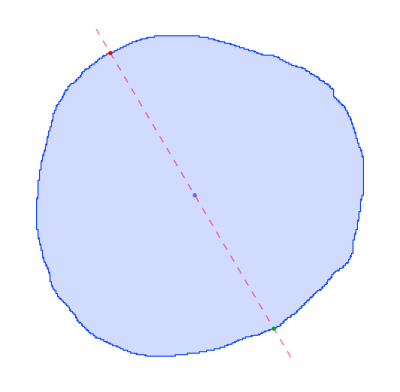
{-Graphics-,{124.966,120.063},{68.4717,215.472},{178.,30.4987},{28.,62.646},{225.442,179.558}}

```mathematica
{graphics,c,c1,c2,c3,c4}=bisectMask[mask1,True]
```

```mathematica
polLine=bresenhamLine[Round[c4],Round[c3]];
Show[ImageRotate[mask1,Pi/2],Graphics[{PointSize[0.035],Orange,Point@c3,Darker@Green,Point@c4,Thick,
Blue,Thickness[0.012],Arrowheads[Large],Arrow@First@TakeDrop[polLine,{45,-50}],
PointSize[0.015],XYZColor[1,0,0,0.5],Point@meanflowF[[All,1]]}]]
```

-Graphics-

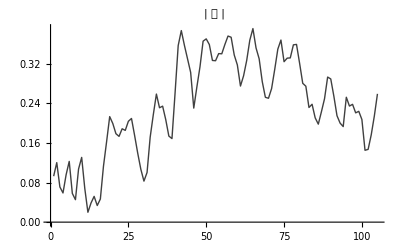

```mathematica
polLineT=First@TakeDrop[polLine,{45,-50}];
upol=Quiet[interpU@@#&/@polLineT];
vpol=Quiet[interpV@@#&/@polLineT];
v=Thread[{upol,vpol}];
truncateFlow=(Norm/@v);
ListLinePlot[truncateFlow,PlotStyle-> {GrayLevel[0.25],Thick},PlotRange->Full,
PlotLabel->Style["| 𝒱 |",Bold,Blue,16]]
```

```mathematica
Clear[fit,model];
```

```mathematica
(*model=k x+b Tanh[p (x-x0)]+d;
fit=NonlinearModelFit[truncateFlow,model,{{k,.1},b,p,d,{x0,20}},x];*)
model=a/(1+Exp[((d-p)-x)/b]);
fit=NonlinearModelFit[truncateFlow,model,{a,{p,30},b,{d,80}},x]
```

FittedModel[0.287527/(1+ⅇ^(«20» («1»)))]

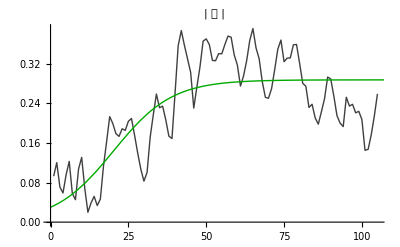

```mathematica
Show[
ListLinePlot[truncateFlow,PlotStyle-> {GrayLevel[0.25],Thick},PlotRange->Full,
PlotLabel->Style["| 𝒱 |",Bold,Blue,16]],Plot[fit[x],{x,0,140},PlotStyle->{Darker@Green,Thick}]
]
```

```mathematica
𝒬=With[{ρ=Quantity[1000, ("Kilograms")/(("Meters")^3 "Seconds")],binningratio=2,resolution=Quantity[0.633, "Micrometers"],L=Quantity[75, "Micrometers"],time=6 60},
ρ*(binningratio*resolution)*(1/L)*(fit[Length@truncateFlow]/time)
]
```

0.0134802 kg/(m^3 s)

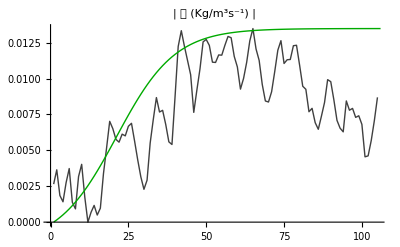

```mathematica
Show[
ListLinePlot[ 𝒬 Rescale[truncateFlow],PlotStyle-> {GrayLevel[0.25],Thick},PlotRange->Full,
PlotLabel->Style["| 𝒬 (Kg/m^3s^-1) |",Bold,Blue,16]],ListLinePlot[𝒬 Rescale@Table[fit[x],{x,0,Length[truncateFlow]}],
PlotStyle->{Darker@Green,Thick}]
]
```